## Systems of Differential Equations and the Matrix Exponential

Student IDs = { #_1,#_2 } | Total Mark = mark | Marker =

## Syntax Reminders

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

For numerical expressions:  exact input ⟹ exact output,  approx input ⟹ approx output

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

### Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively one can use a Palette such as the Basic Math Assistant.

### Replacement Rules

Solutions to equations are returned as a list of lists of replacement rules:

```mathematica
sol=Solve[{a x^2+b y==0,c x+d y==0},{x,y}]
```

{{y→0,x→0},{y→-(b c^2)/(a d^2),x→(b c)/(a d)}}

To use the solutions, the ReplaceAll (/.) command is used. Here we substitute both solutions into both equations:

```mathematica
{a x^2+b y==0,c x+d y==0}/.sol
```

(True | True
True | True)

Substitute the second (or Last) solution into the variable x:

```mathematica
x/.sol⟦2⟧
```

(b c)/(a d)

Remove this definition:

```mathematica
Remove[sol]
```

### Protected Symbols

Certain symbols, such as D (which denotes the partial derivative) are protected:

```mathematica
D=2
```

Set::wrsym: Symbol D is Protected.

2

If one uses lower-case letters this problem is avoided.

An alternative is to use, say, script letters, available in the SpecialCharacters palette:

```mathematica
𝒟=2
```

2

Note that most special characters have Esc aliases (or keyboard shortcuts):  eg  𝒟 ← EscscDEsc,  while  𝔻 ← EscdsDEsc  etc…

### Basic List Operations

One can extract parts of an expression expr using Part or using the shorthand form expr[[n]] or expr⟦n⟧, with ⟦ ← Esc[[Esc :

```mathematica
{x,y,z}⟦2⟧
```

2

One can extract multiple entries using a list of indices:

```mathematica
{x,y,z}⟦{2,3,2,1}⟧
```

{y,z,y,x}

A matrix is a list of lists (rows).

Here is the first row of the matrix (a | b
c | d)={{a,b},{c,d}} :

```mathematica
({{a, b}, {c, d}})⟦1⟧
```

{a,b}

Here is the (2,1) element:

```mathematica
({{a, b}, {c, d}})⟦2,1⟧
```

Swap the first and second rows:

```mathematica
({{a, b}, {c, d}})⟦{2,1}⟧
```

The easiest way of swapping columns is to take the Transpose of the matrix first.

### Generating Matrices

One can construct matrices in a variety of ways. For now, we will do it either:

by hand, typing in a list of lists;

using the Basic Math Assistant palette;

using Insert ▸ Table/Matrix ▸ New…  ;

or using the Table command.

Construct a 2×3 matrix as a list of lists:

```mathematica
{{a,b,c},{d,e,f}}
```

(a | b | c
d | e | f)

Use Table to construct a general 4×6 matrix:

```mathematica
Table[Subscript[a, i,j],{i,4},{j,6}]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5) | a_(1,6)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5) | a_(2,6)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5) | a_(3,6)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5) | a_(4,6))

If you are not using TraditionalForm for output, you can use MatrixForm to display matrices:

```mathematica
MatrixForm@%
```

### Defining Functions

Define the function, f(x)=x^2+1:

```mathematica
f[x_]:=x^2+1
```

Note that the symbol f went from blue = undefined to black = defined.

Here is f(2):

```mathematica
f[2]
```

5

Here is f({x,y}):

```mathematica
f[{x,y}]
```

{x^2+1,y^2+1}

To see what definitions are associated with a symbol, use ?

```mathematica
?f
```

Global`f

f[x_]:=x^2+1

Clear this definition:

```mathematica
Clear[f]
```

The symbol f has now returned to being blue:

```mathematica
?f
```

Global`f

### Defining Vector Functions

Define g(x,y)=(x y,x^2-y^2), a vector function (or map) g:ℝ^2→ℝ^2:

```mathematica
g[{x_,y_}]:={x y,x^2-y^2}
```

Compute g(a,b):

```mathematica
g[{a,b}]
```

{a b,a^2-b^2}

Note that g takes a vector and returns a vector. This is useful when composing such functions.

Compute g∘g(x,y):

```mathematica
g@g[{x,y}]//Simplify
```

{x y (x^2-y^2),-x^4+3 x^2 y^2-y^4}

Remove this definition:

```mathematica
Clear[g]
```

## Introduction

In this assignment we are going to consider systems of differential equations,

x'(t)==A.x(t)

where x(t) is a vector and A is a (square) matrix.

Substituting x(t)→u exp(λ t) into this equation one finds that the differential equation is solved if λ u=A u, i.e. if u is an eigenvector of A with corresponding eigenvalue λ. For diagonalizable matrices this is all we need to find a general solution of the system.

A simple example of an invertible matrix that is not diagonalizable is (1 | 1
0 | 1). Can you see why?

However one can make the solution look neat, give a fundamental matrix for use in the variation of parameters formulae for nonhomogeneous d.e.s, and give a formula which is true for all matrices, not just diagonalizable ones, by writing the solution:

x(t)==exp(t A). x(0).

where exp(t A) is the matrix exponential defined by

exp(A)==∑_(n=0)^∞ A^n/(n!)

where A^0==ℐ and A^2=A.A etc. The MatrixExp command computes the matrix exponential.

## Solving a system of linear differential equations using DSolve

Consider the linear system of differential equations

x_1'(t)==-2x_1(t)-x_2(t),
x_2'(t)==-x_1(t)-2x_2(t).

Use DSolve to find the general solution of the system (Section.DisplayFormulaNumbered). [2 Marks]

Solution

```mathematica
eqns={Subscript[x, 1]'[t]==-2 Subscript[x, 1][t]-Subscript[x, 2][t],Subscript[x, 2]'[t]==-Subscript[x, 1][t]-2 Subscript[x, 2][t]};
```

```mathematica
solGS=First@DSolve[eqns,{Subscript[x, 1][t],Subscript[x, 2][t]},t]
```

{x_1(t)→1/2 c_1 ⅇ^(-3 t) (ⅇ^(2 t)+1)-1/2 c_2 ⅇ^(-3 t) (ⅇ^(2 t)-1),x_2(t)→1/2 c_2 ⅇ^(-3 t) (ⅇ^(2 t)+1)-1/2 c_1 ⅇ^(-3 t) (ⅇ^(2 t)-1)}

Apply the initial value conditions x_1(0)==1 and x_2(0)==2 to the general solution. Compare your solution to that obtained directly using DSolve. [2 Marks]

Solution

Apply the initial value conditions x_1(0)==1 and x_2(0)==2 to the general solution:

```mathematica
ics={Subscript[x, 1][0]==1,Subscript[x, 2][0]==2};
```

```mathematica
ics/.(solGS/.t->0)
```

{c_1==1,c_2==2}

```mathematica
%/.Equal->Rule
```

{c_1→1,c_2→2}

```mathematica
solGS/.%//ExpandAll
```

{x_1(t)→(3 ⅇ^(-3 t))/2-ⅇ^-t/2,x_2(t)→(3 ⅇ^(-3 t))/2+ⅇ^-t/2}

Compare this solution to that obtained using DSolve:

```mathematica
solIC=First@DSolve[Join[eqns,ics],{Subscript[x, 1][t],Subscript[x, 2][t]},t]//ExpandAll
```

{x_1(t)→(3 ⅇ^(-3 t))/2-ⅇ^-t/2,x_2(t)→(3 ⅇ^(-3 t))/2+ⅇ^-t/2}

## Graphing solutions to systems of differential equations

Given a system of two or (or more) differential equations, e.g.,

y'_1(t)==f(t,y_1,y_2),
y'_2(t)==g(t,y_1,y_2),

it is easy to plot out solutions, usually from an NDSolve, in various different ways.

Compute the solutions to the system of equations from Exercise Exercise satisfying the initial conditions

x_1(0)==a,
x_2(0)==b,

for arbitrary a and b.

Graph the solutions for various values of a and b as a Plot against time using Manipulate. [2 Marks]

Display a ParametricPlot of {x_1,x_2} as a function of time. [1 Mark]

Solution

Solve the system of differential equations for the initial conditions with a and b arbitrary.

```mathematica
ics={Subscript[x, 1][0]==a,Subscript[x, 2][0]==b};
```

```mathematica
DSolve[Join[eqns,ics],{Subscript[x, 1][t],Subscript[x, 2][t]},t]
```

{{x_1(t)→-1/2 ⅇ^(-3 t) (a (-ⅇ^(2 t))-a+b ⅇ^(2 t)-b),x_2(t)→-1/2 ⅇ^(-3 t) (a ⅇ^(2 t)-a-b ⅇ^(2 t)-b)}}

Define x_1 and x_2 as functions of t and the parameters {a,b}:

```mathematica
{Subscript[x, 1][t_,{a_,b_}],Subscript[x, 2][t_,{a_,b_}]}={Subscript[x, 1][t],Subscript[x, 2][t]}/.First[%]
```

{-1/2 ⅇ^(-3 t) (a (-ⅇ^(2 t))-a+b ⅇ^(2 t)-b),-1/2 ⅇ^(-3 t) (a ⅇ^(2 t)-a-b ⅇ^(2 t)-b)}

Use Manipulate to graph the solutions of the system for various a and b.

```mathematica
Manipulate[Plot[{Subscript[x, 1][t,{a,b}],Subscript[x, 2][t,{a,b}]},{t,0,2},
AxesLabel->{t,x},
PlotRange->{-2,4}],
{{a,1},0,3},
{{b,2},0,3},
SaveDefinitions->True]
```

Instead of using sliders, we can use a Locator for each initial value, and use Tooltip to identify which curve is which:

```mathematica
Manipulate[Plot[{Tooltip[Subscript[x, 1][t,{a,b}],Subscript[x, 1]],Tooltip[Subscript[x, 2][t,{a,b}],Subscript[x, 2]]},{t,0,2},
AxesLabel->{t,x},
PlotRange->{-2,4}],
{{a,{0,1}},{0,-4},{0,8},Locator},
{{b,{0,2}},{0,-4},{0,8},Locator},
SaveDefinitions->True]
```

Display a ParametricPlot of x_1 versus x_2 as a function of time. Use a Locator for the point p={a,b}:

```mathematica
Manipulate[ParametricPlot[{Subscript[x, 1][t,p],Subscript[x, 2][t,p]},{t,0,12},
AxesLabel->{t,x},
PlotRange->3],
{{p,{1,2}},{-3,-3},{3,3},Locator},
SaveDefinitions->True]
```

Plot the direction field of the system (Section.DisplayFormulaNumbered) usingStreamDensityPlot. Use Show to superimpose the solutions of the initial value problems upon the direction field, using Manipulate to vary the values of a and b. [2 Marks]

Solution

Determine the components of the direction field:

```mathematica
components=Last/@eqns/.f_[t]->f
```

{-2 x_1-x_2,-x_1-2 x_2}

Display the direction field using StreamDensityPlot:

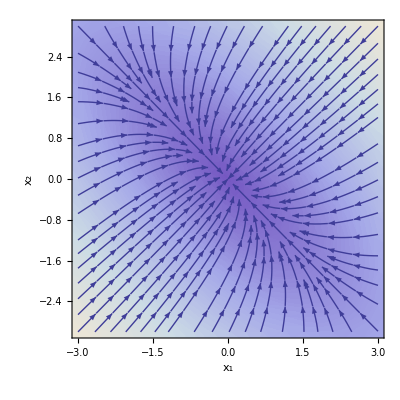

```mathematica
sdp=StreamDensityPlot[components,{Subscript[x, 1],-3,3},{Subscript[x, 2],-3,3},AxesLabel->{Subscript[x, 1],Subscript[x, 2]},Axes->True,PlotRange->3]
```

Display the solutions of the initial value problems using Manipulate to vary the values of a and b:

```mathematica
Manipulate[Show[sdp,
ParametricPlot[{Subscript[x, 1][t,p],Subscript[x, 2][t,p]},{t,0,10},PlotStyle->Red]],
{{p,{1,2}},{-3,-3},{3,3},Locator},
SaveDefinitions->True]
```

Plot the parametric solution {t,x_1(t),x_2(t)} in three-dimensions using ParametricPlot3D and use Manipulate to vary the values of a and b. [2 Marks]

Solution

Here is a ParametricPlot3D of {t,x_1(t),x_2(t)} as a function of time:

```mathematica
Manipulate[Show[ParametricPlot3D[{t,Subscript[x, 1][t,p],Subscript[x, 2][t,p]},{t,0,6},PlotRange->{{-0.2,6},{-3.2,3.2},{-3.2,3.2}}],Graphics3D@Sphere[{t,Subscript[x, 1][t,p],Subscript[x, 2][t,p]}/.t->0,0.1]],
{{p,{1,2}},{-3,-3},{3,3}},
SaveDefinitions->True]
```

## Matrix exponentials and system (DisplayFormulaNumbered)

With

```mathematica
A=({{-2, -1}, {-1, -2}});
```

and

```mathematica
x(t_):=({{Subscript[x, 1](t)}, {Subscript[x, 2](t)}})
```

the system of differential equations (DisplayFormulaNumbered) can be written x'(t)== A.x(t):

```mathematica
x'(t)==A.x(t)
```

(x_1'(t)
x_2'(t))==(-2 x_1(t)-x_2(t)
-x_1(t)-2 x_2(t))

Obtain the eigenvalues, λ, of A and compute exp(A t) using MatrixExp. The solution to the initial value problem is x(t)==exp(A t).x(0). Compare this solution to the initial value problem obtained in Exercise Exercise where we we have used x(0)={1,2}. They should be the same. [2 Marks]

Solution

Compute the eigenvalues, λ, of A:

```mathematica
λList=Eigenvalues[A]
```

{-3,-1}

Compute exp(A t) using MatrixExp:

```mathematica
expAt=Expand[MatrixExp[A t]]
```

(ⅇ^(-3 t)/2+ⅇ^-t/2 | ⅇ^(-3 t)/2-ⅇ^-t/2
ⅇ^(-3 t)/2-ⅇ^-t/2 | ⅇ^(-3 t)/2+ⅇ^-t/2)

Note the occurence of eigenvalues, λ, times t in the arguments of the exponentials.

Here is the solution to the initial value problem x(t)==exp(A t).x(0) for x(0)={1,2}:

```mathematica
expAt.{1,2}//Expand
```

{(3 ⅇ^(-3 t))/2-ⅇ^-t/2,(3 ⅇ^(-3 t))/2+ⅇ^-t/2}

This agrees with the solution to the initial value problem obtained in Exercise Exercise:

```mathematica
solIC//Expand
```

{x_1(t)→(3 ⅇ^(-3 t))/2-ⅇ^-t/2,x_2(t)→(3 ⅇ^(-3 t))/2+ⅇ^-t/2}

As an aside, you can determine the matrix from “polynomial” equations using CoefficientArrays.

```mathematica
eqns
```

{x_1'(t)==-2 x_1(t)-x_2(t),x_2'(t)==-x_1(t)-2 x_2(t)}

```mathematica
CoefficientArrays[Last/@eqns,{Subscript[x, 1][t],Subscript[x, 2][t]}]//Normal
```

(0 | 0
{-2,-1} | {-1,-2})

```mathematica
Last[%]
```

(-2 | -1
-1 | -2)

Visualize the solution x(t)==exp(A t).x(0) for various initial conditions, x(0), (Hint: Have a look at the last of the LocatorPane “Neat Examples” and the ClickPane applications for closely related examples). [2 Marks]

Solution

We can visualize solutions to x(t)==exp(A t).x(0) for Dynamic values of the initial condition, x(0), provided by the location of a mouse click, using LocatorPane. Using Alt+click (⌘+click under MacOS) adds additional initial values:

```mathematica
DynamicModule[{pts={{1,2}},𝒜=({{-2, -1}, {-1, -2}})},LocatorPane[Dynamic[pts],Dynamic[ParametricPlot[Evaluate[(x↦MatrixExp[𝒜 t].x)/@pts],{t,0,10},PlotRange->3]],LocatorAutoCreate->True]]
```

And we can keep track of all solutions as we go using ClickPane. Values of the initial condition, x(0), are provided by the location of a mouse click:

```mathematica
DynamicModule[{s={},𝒜=({{-2, -1}, {-1, -2}})},ClickPane[Framed@Dynamic@ParametricPlot[s,{t,0,10},PlotRange->5],x↦AppendTo[s,MatrixExp[𝒜 t].x]]]
```

## Matrix exponentials for some simple matrices

Show that the matrix exponential exp(t S), with

```mathematica
S=({{0, -1}, {1, 0}});
```

is orthogonal. [2 Marks]

Solution

```mathematica
expSt=MatrixExp[t S]
```

(cos(t) | -sin(t)
sin(t) | cos(t))

A matrix is orthogonal if Transpose[A].A==A.Transpose[A]==ℐ:

```mathematica
Simplify[Transpose[expSt].expSt]
```

(1 | 0
0 | 1)

As this is the (2×2) identity matrix, exp(t S)—which is the 2D rotation matrix—is orthogonal.

Consider the matrix

```mathematica
ℳ=({{0, 0, 1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, -1, 0, 0}});
```

Show that ℳ^2=ℐ. Compute and simplify exp(t ℳ) and verify that it is of the form f(t) I+g(t) ℳ for some functions f and g. [3 Marks]

Solution

```mathematica
ℳ.ℳ
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
expℳ=FullSimplify[MatrixExp[t ℳ]]
```

(cosh(t) | 0 | sinh(t) | 0
0 | cosh(t) | 0 | -sinh(t)
sinh(t) | 0 | cosh(t) | 0
0 | -sinh(t) | 0 | cosh(t))

So we can read off the result that we wanted:

```mathematica
Solve[expℳ==f(t) IdentityMatrix[4]+ℳ g(t),{f(t),g(t)}]
```

{{f(t)→cosh(t),g(t)→sinh(t)}}

Consider the tridiagonal matrix

```mathematica
𝒯=({{0, -1, 0}, {-1, 0, -1}, {0, -1, 0}});
```

Determine the eigenvalues of 𝒯 and show that 𝒯^3==λ^2 𝒯 for λ≠0. [1 Marks]

Verify that exp(t 𝒯) is equal to (ℐ-λ^-2 𝒯^2 )+cosh(λ t)  λ^-2 𝒯^2+sinh(λ t)  λ^-1 𝒯. [2 Marks]

Solution

```mathematica
Eigenvalues[𝒯]
```

{-√2,√2,0}

```mathematica
𝒯.𝒯.𝒯==λ^2 𝒯/.{{λ->-√2},{λ->√2}}
```

{True,True}

```mathematica
exp𝒯=MatrixExp[t 𝒯]//FullSimplify//TrigReduce
```

(1/2 (cosh(√2 t)+1) | -(sinh(√2 t))/(√2) | 1/2 (cosh(√2 t)-1)
-(sinh(√2 t))/(√2) | cosh(√2 t) | -(sinh(√2 t))/(√2)
1/2 (cosh(√2 t)-1) | -(sinh(√2 t))/(√2) | 1/2 (cosh(√2 t)+1))

exp(t 𝒯) can be decomposed as follows:

```mathematica
exp𝒯==1/2({{1, 0, -1}, {0, 0, 0}, {-1, 0, 1}})+1/2({{1, 0, 1}, {0, 2, 0}, {1, 0, 1}}) cosh(√2 t)-1/(√2)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}) sinh(√2 t)//Expand
```

True

Compute 𝒯^2==𝒯.𝒯:

```mathematica
𝒯.𝒯
```

(1 | 0 | 1
0 | 2 | 0
1 | 0 | 1)

The matrix decomposition of exp(t 𝒯) can be extracted using Variables and CoefficientArrays:

```mathematica
Variables[exp𝒯]
```

{cosh(√2 t),sinh(√2 t)}

```mathematica
coefs=Normal@CoefficientArrays[exp𝒯,Variables[exp𝒯]];
```

```mathematica
First[coefs]
```

(1/2 | 0 | -1/2
0 | 0 | 0
-1/2 | 0 | 1/2)

```mathematica
Map[First,Last[coefs],{2}]
```

(1/2 | 0 | 1/2
0 | 1 | 0
1/2 | 0 | 1/2)

```mathematica
Map[Last,Last[coefs],{2}]
```

(0 | -1/(√2) | 0
-1/(√2) | 0 | -1/(√2)
0 | -1/(√2) | 0)

```mathematica
exp𝒯==((IdentityMatrix[3]-λ^-2 𝒯.𝒯 )+cosh(λ t)  λ^-2 𝒯.𝒯+sinh(λ t)  λ^-1 𝒯)/.λ->√2//Simplify
```

True

Aside

One doesn't need Mathematica to do this computation. In fact the formula is true for any matrix M satisfying M^3==λ^2 M. There are several ways to establish this. One way is to use the series for exp(M t), collecting terms with like powers of M and noting that the even power terms are all (either the identity) or multiples of the square of M, whicle the odd powers of M are all multiples of M.

Expand out the matrix exponential ⅇ^(M t) and apply the relation M^3== λ^2 M:

ⅇ^(M t)==∑_(n=0)^∞ (M^n t^n)/(n!)==ℐ+M t+1/2 M^2 t^2+λ^2 M t^3/(3!)+λ^2 M^2 t^4/(4!)+λ^2 M^5 t^5/(5!)+λ^4 M^2 t^6/(6!)+λ^4 M^2 t^6/(6!)+⋯

Implement this relation implicitly using pattern-matching:

```mathematica
exp(M t)+O[t]^15//.M^(n_/;n≥3):>λ^2 M^(n-2)
```

1+M t+(M^2 t^2)/2+1/6 λ^2 M t^3+1/24 λ^2 M^2 t^4+1/120 λ^4 M t^5+1/720 λ^4 M^2 t^6+(λ^6 M t^7)/5040+(λ^6 M^2 t^8)/40320+(λ^8 M t^9)/362880+(λ^8 M^2 t^10)/3628800+(λ^10 M t^11)/39916800+(λ^10 M^2 t^12)/479001600+(λ^12 M t^13)/6227020800+(λ^12 M^2 t^14)/87178291200+O(t^15)

Collect even and odd powers of M:

```mathematica
Collect[%,M]
```

M^2 ((λ^12 t^14)/87178291200+(λ^10 t^12)/479001600+(λ^8 t^10)/3628800+(λ^6 t^8)/40320+(λ^4 t^6)/720+(λ^2 t^4)/24+t^2/2)+M ((λ^12 t^13)/6227020800+(λ^10 t^11)/39916800+(λ^8 t^9)/362880+(λ^6 t^7)/5040+(λ^4 t^5)/120+(λ^2 t^3)/6+t)+1

Verify that ⅇ^(M t)==(ℐ-λ^-2 M^2 )+cosh(λ t)  λ^-2 M^2+sinh(λ t)  λ^-1 M:

```mathematica
%%-((1-M^2 λ^-2)+M^2 λ^-2 cosh(λ t)+M λ^-1 sinh(λ t))
```

O(t^15)

Alternatively, the matrix Φ (t) such that

Φ'(t)==𝒯.Φ(t)
Φ (0)==ℐ

is exp(t 𝒯).

So we check that the given solution,

```mathematica
Clear[𝒯]
```

```mathematica
Φ(t_):=(ℐ-λ^-2 𝒯^2 )+cosh(λ t)  λ^-2 𝒯^2+sinh(λ t)  λ^-1 𝒯
```

satisfies the initial condition

```mathematica
Φ(0)==ℐ
```

True

and the differential equation

```mathematica
Expand[Φ'(t)==𝒯 Φ(t)]/.𝒯 ℐ ->𝒯
```

(𝒯^2 sinh(λ t))/λ+𝒯 cosh(λ t)==(𝒯^3 cosh(λ t))/λ^2+(𝒯^2 sinh(λ t))/λ-𝒯^3/λ^2+𝒯

under the condition that 𝒯^3==λ^2 𝒯

```mathematica
%/.𝒯^3->λ^2 𝒯//Simplify
```

True